```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0
```

Y^(0,1)[x,t]-𝒟 Y^(2,0)[x,t]==0

```mathematica
f0[t_]:=a+b Sin[ν t]
```

```mathematica
f1[t_]:=a
```

```mathematica
g0[x_]:=a
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→a-b (-1+x) Sin[t ν]+-(2 b 𝒟 ν (-ⅇ^(-π^2 t 𝒟 K[1]^2) π^2 𝒟 K[1]^2+π^2 𝒟 Cos[t ν] K[1]^2+ν Sin[t ν]) Sin[π x K[1]])/(π K[1] (ν^2+π^4 𝒟^2 K[1]^4))K[1]1∞}}

```mathematica
Yf[x_,t_]:=Y[x,t]/.sol[[1]]
```

```mathematica
Yf[x_,t_]:=a-b(x-1) Sin[ν t]-∑_(k=1)^20 (2b 𝒟 ν(-ⅇ^(-π^2 t 𝒟 k^2) π^2 𝒟 k^2+π^2 𝒟 Cos[t ν] k^2+ν Sin[t ν]) Sin[π x k])/(π k (ν^2+π^4 𝒟^2 k^4))
```

```mathematica
a=0.5;b=0.1;ν=2π;𝒟=1;
```

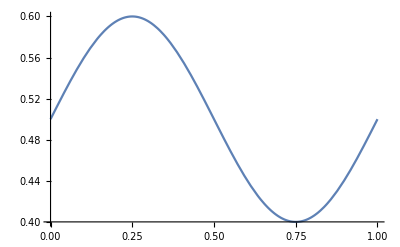

```mathematica
Plot[f0[t],{t,0,1}]
```

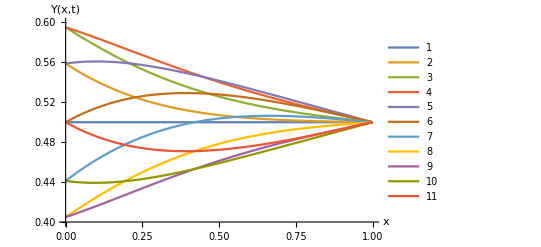

```mathematica
Plot[{Yf[x,0],Yf[x,0.1],Yf[x,0.2],Yf[x,0.3],Yf[x,0.4],Yf[x,0.5],Yf[x,0.6],Yf[x,0.7],Yf[x,0.8],Yf[x,0.9],Yf[x,1]},{x,0,1},PlotRange->{0.4,0.6},AxesLabel->{"x","Y(x,t)"},PlotLegends->Automatic]
```